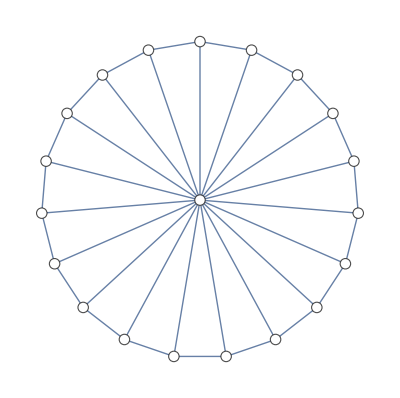

```mathematica
Clear[ImportTikZGraph]

ImportTikZGraph[file_String]:=Module[{tikzCode,lines,nodes,edges,line,parts,nodeID,xCoord,yCoord,startNode,endNode,g},(*Import the TikZ code from the file*)tikzCode=Import[file,"Text"];
(*Initialize lists for nodes and edges*)nodes={};
edges={};
(*Split the TikZ code into lines*)lines=StringSplit[tikzCode,"\n"];
(*Extract node information*)For[i=1,i<=Length[lines],i++,line=StringTrim[lines[[i]]];
If[StringStartsQ[line,"\\node"],(*Extract node ID and coordinates*)parts=StringCases[line,"\\node ["~~___~~"] ("~~nodeID:DigitCharacter..~~") at ("~~x:(DigitCharacter|"."|"-"|"E")..~~", "~~y:(DigitCharacter|"."|"-"|"E")..~~") {};":>{nodeID,x,y}];
If[Length[parts]>0,nodeID=ToExpression[parts[[1,1]]];
xCoord=ToExpression[parts[[1,2]]];
yCoord=ToExpression[parts[[1,3]]];
AppendTo[nodes,nodeID->{xCoord,yCoord}];];];];
(*Extract edge information*)For[i=1,i<=Length[lines],i++,line=StringTrim[lines[[i]]];
If[StringStartsQ[line,"\\draw"],(*Extract the start and end nodes of edges*)parts=StringCases[line,"\\draw ("~~startNode:DigitCharacter..~~") to ("~~endNode:DigitCharacter..~~");":>{startNode,endNode}];
If[Length[parts]>0,startNode=ToExpression[parts[[1,1]]];
endNode=ToExpression[parts[[1,2]]];
AppendTo[edges,UndirectedEdge[startNode,endNode]];];];];
(*Create the graph from extracted edges and node positions*)g=Graph[edges,VertexCoordinates->nodes,VertexStyle->GrayLevel[1],VertexSize->Medium];
(*Return the graph*)g]

graph=ImportTikZGraph["scaled_graph_output.tikz"]
```